```mathematica
Quit[]
```

```mathematica
<<TRQS`
```

Package TRQS version 0.2.0 (last modification: 07/05/2012).

INFO: Using Quantis as a source of randomness.

Note: You should configure this backend with QuantisSetDevice function by providing information about the type and id of the used Quantis device.

Note: By default the package will use a USB Quantis device with id set to 0.

```mathematica
QuantisSetDevice["USB",0]
```

Using Quantis device: type=USB, id=0

```mathematica
QuantisGetDevice[]
```

Using Quantis device: type=USB, id=0

```mathematica
Table[TrueRandomReal[{1,4}],{ 300}]
```

{2.25697,2.95499,2.27858,3.37963,1.54966,3.45168,1.77759,2.4552,2.02485,2.58733,3.38355,2.02984,1.50645,2.1511,2.53944,3.0019,1.1947,1.73383,3.24547,1.73609,1.5204,3.62506,1.98899,3.5642,3.39438,3.21119,3.84051,3.94442,1.59931,1.33795,2.16941,2.61405,2.13855,2.32361,3.19645,1.9188,1.87224,2.6299,2.12468,1.11315,3.01262,1.66904,2.69748,1.95363,1.01685,3.43371,2.83151,1.4417,1.50524,3.44872,2.39056,2.93206,1.67056,1.09744,3.52414,3.84433,3.45687,1.67423,3.62075,3.19217,2.24523,3.95858,2.32516,2.67572,3.16994,3.47873,1.99023,3.15947,1.76776,3.67296,2.45771,1.04045,3.71021,1.12928,1.9917,1.19511,2.95731,1.10821,3.25871,2.16652,2.60674,3.06773,2.56434,3.79527,2.9026,2.50821,1.53875,1.84833,3.33505,2.67226,2.11684,3.53813,3.53638,1.98117,3.76744,1.82888,1.65588,3.85364,3.10601,2.76701,2.64772,2.63558,2.65999,3.93303,1.34146,1.63487,1.91304,1.40509,2.77108,2.66222,2.29981,3.89645,3.96582,1.1429,1.67963,1.8165,3.97457,1.53919,3.80534,3.23009,3.89445,1.48026,2.99806,1.29698,2.4529,2.34649,3.31997,1.11083,3.55633,2.69552,2.72127,3.05127,3.23555,1.96028,3.08014,2.52505,3.67602,3.42447,2.73122,1.0354,1.58272,2.24869,2.99874,2.50574,2.48117,2.22838,3.46033,1.7555,2.00118,3.44383,3.64438,1.49491,1.29692,3.28363,2.23153,3.63293,3.52072,2.21014,2.13944,1.69728,2.10454,2.49622,2.73277,3.16866,2.19716,1.22628,1.01593,2.01967,3.51987,2.55187,2.36078,2.50944,1.75457,3.04038,2.45935,2.12579,1.73558,3.49811,3.39364,2.92106,3.32988,1.13406,1.64397,3.80458,2.6244,3.13345,2.06685,2.41057,2.36204,2.75011,3.63494,1.39921,2.83493,1.71006,1.44436,3.90314,1.03027,1.71512,2.78073,3.94966,3.51803,1.22884,2.04466,3.39946,1.42727,3.41527,3.39473,1.84345,2.73974,2.40976,1.62566,3.40906,1.20807,1.73704,1.28054,2.10132,1.73427,2.87976,3.83388,3.36945,1.08249,2.1494,1.53726,2.64808,3.44883,3.05575,2.40327,1.79768,1.94904,3.06621,2.51147,1.5001,1.11489,2.77393,1.79686,1.59317,3.66109,3.00573,2.88147,1.68406,3.73572,3.79225,1.01673,2.09692,3.59514,3.0168,1.5385,3.19169,3.77897,1.70351,1.42598,2.85022,2.74488,1.90028,2.0116,2.65955,1.47852,2.59416,1.10428,1.81409,2.82876,2.8946,3.54433,2.48029,2.85069,1.77357,3.86296,3.78198,2.93111,1.91477,2.06931,2.13581,2.64984,1.73543,2.68312,1.8344,3.81647,3.69445,3.8162,3.84223,1.47929,2.74303,3.51395,1.44821,3.79812,2.72999,2.15675,1.85841,3.63398,1.88973,1.95776,1.69605,2.84183,2.25603,1.43381,1.13952,3.50238,3.67069,1.28082,2.39999}

```mathematica
TrueRandomInteger[{1,10},4]
```

{1,6,2,5}

```mathematica
QuantisGetSerialNumber[]
```

080259A410

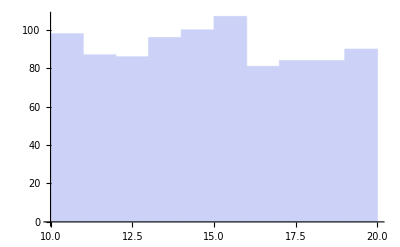

```mathematica
Histogram[TrueRandomInteger[{10,20},1000]]
```